# Équation d'onde classique

## Corde tendue fixée au point x = 0 et libre au point x = L

## Exemple 1

## Caracteristique de la corde

```mathematica
ClearAll["Global`*"]
```

Longueur de la corde (m)

```mathematica
L:=1
```

Masse de la corde (Kg)

```mathematica
m:=0.1
```

Tension dans la corde (N)

```mathematica
T:=10
```

Densité linéaire uniforme (Kgm^-1)

```mathematica
μ=m/L
```

0.1

Vitesse de phase (ms^-1)

```mathematica
v=√(T/μ)
```

10.

## Les conditions aux frontières

```mathematica
ψ[0,t_]:=0;
```

```mathematica
ψ[L,t_]:=0;
```

## Les conditions initiales

La forme initiale :

```mathematica
ψ[x_,0]:=x
```

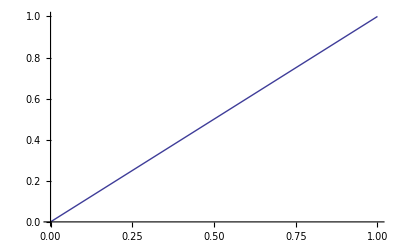

```mathematica
Plot[ψ[x,0],{x,0,L}]
```

La vitesse initiale :

```mathematica
ψ'[x_,0]:=0
```

## Solution

Les valeures propres de l'équation de Helmhotz pour X[x]

```mathematica
Subscript[k, n_]:=((n-1/2) π)/L
```

Les fonctions propres de l'équation de Helmhotz pour X[x]

```mathematica
Subscript[X, n_][x_]:=Sin[Subscript[k, n]  x]
```

Les valeures propres  de l'équation de Helmhotz pour T[t]

```mathematica
Subscript[ω, n_]=Subscript[k, n] v
```

31.4159 (-1/2+n)

Les coéficients A_n et B_n

```mathematica
Subscript[A, n_]=2/L ∫_0^L ψ[x,0]Sin[Subscript[k, n] x]ⅆx
```

(2 (-4 Cos[n π]+2 (1-2 n) π Sin[n π]))/(π-2 n π)^2

```mathematica
Subscript[B, n_]=2/(Subscript[ω, n] L) ∫_0^L ψ'[x,0]Sin[Subscript[k, n] x]ⅆx
```

0.

Les fonctions propres  de l'équation de Helmhotz pour T[t]

```mathematica
Subscript[T, n_][t_]:=Subscript[A, n] Cos[Subscript[ω, n] t]+Subscript[B, n] Sin[Subscript[ω, n] t]
```

Les composantes de la fonction d'onde

```mathematica
Subscript[ψ, n_][x_,t_]=Subscript[X, n][x]Subscript[T, n][t]
```

(0.+(2 Cos[31.4159 (-1/2+n) t] (-4 Cos[n π]+2 (1-2 n) π Sin[n π]))/(π-2 n π)^2) Sin[(-1/2+n) π x]

Longueur d' onde des composantes de la fonction d'onde

```mathematica
Subscript[λ, n_]=(2π)/Subscript[k, n]
```

2/(-1/2+n)

Fréquence des composantes de la fonction d'onde

```mathematica
Subscript[ν, n_]=v/Subscript[λ, n]
```

5. (-1/2+n)

Fonction d' onde

```mathematica
ψ[x_,t_]=∑_(n=1)^6 Subscript[ψ, n][x,t]
```

(0.+(8 Cos[15.708 t])/π^2) Sin[(π x)/2]+(0.-(8 Cos[47.1239 t])/(9 π^2)) Sin[(3 π x)/2]+(0.+(8 Cos[78.5398 t])/(25 π^2)) Sin[(5 π x)/2]+(0.-(8 Cos[109.956 t])/(49 π^2)) Sin[(7 π x)/2]+(0.+(8 Cos[141.372 t])/(81 π^2)) Sin[(9 π x)/2]+(0.-(8 Cos[172.788 t])/(121 π^2)) Sin[(11 π x)/2]

## Tableau

```mathematica
expr1:=n
```

```mathematica
expr2:=Subscript[ψ, n][x,0]
```

```mathematica
expr3:=Plot[Subscript[ψ, n][x,0],{x,0,L},Frame->True]
```

```mathematica
expr4:=Subscript[λ, n]
```

```mathematica
table:=Table[{expr1,expr2,expr3,expr4},{n,1,6}]
```

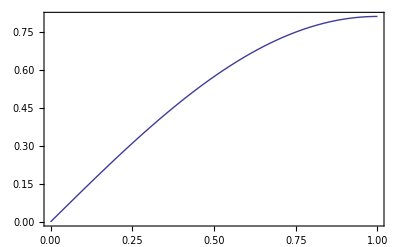
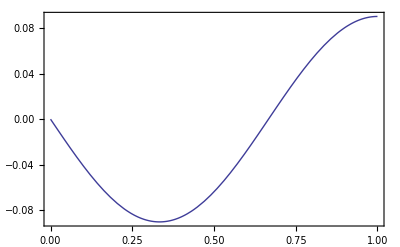
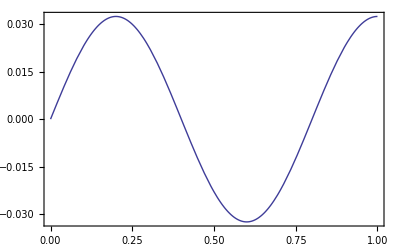
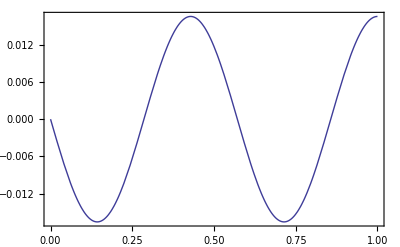
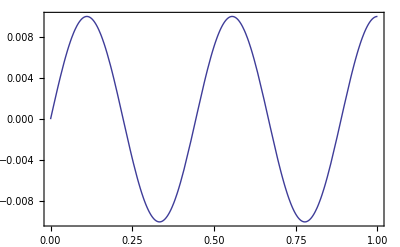
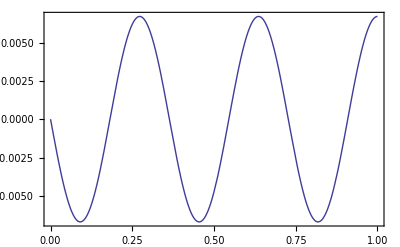
1 | 0.810569 sin((π x)/2) | -Graphics- | 4
2 | -0.0900633 sin((3 π x)/2) | -Graphics- | 4/3
3 | 0.0324228 sin((5 π x)/2) | -Graphics- | 4/5
4 | -0.0165422 sin((7 π x)/2) | -Graphics- | 4/7
5 | 0.010007 sin((9 π x)/2) | -Graphics- | 4/9
6 | -0.00669892 sin((11 π x)/2) | -Graphics- | 4/11

```mathematica
Grid[table,Frame->All]//TraditionalForm
```

## Visualisation

### Représentation des modes normeaux

```mathematica
Manipulate[Plot[Subscript[ψ, Mode][x,t],{x,0,L},PlotRange->{-N[Subscript[A, Mode]+Subscript[B, Mode]],N[Subscript[A, Mode]+Subscript[B, Mode]]},Frame->True],{Mode,{1,2,3,4,5,6}},{t,0,(4L)/v}]
```

### Représentation de superpositions des modes normeaux

```mathematica
Manipulate[Plot[ψ[x,t],{x,0,L},PlotRange->{-1.1,1.1},Frame->True],{t,0,(4L)/v}]
```